```mathematica
zz[μ_,L_]:=NIntegrate[1/(Exp[μ L Cosh[τ]]-1),{τ,-∞,∞},WorkingPrecision->20]
```

```mathematica
zmu2=Table[{i,Exp[-zz[1,i]]},{i,1,40}]
```

{{1,0.3094977904222907765},{2,0.77652330650203599092},{3,0.930462627621664026878},{4,0.977637075377313136018},{5,0.9926094907804766098008},{6,0.9975107041845772330028},{7,0.99915021709958766523702},{8,0.99970703150575089580329},{9,0.99989823361422771183162},{10,0.999964439359372021247653},{11,0.999987513888607772741822},{12,0.9999955983396749781187014},{13,0.9999984430899399422096812},{14,0.9999994477256616000654935},{15,0.99999980360924698717717205},{16,0.999999930011763580331202161},{17,0.999999975010671525482592147},{18,0.9999999910624932687490788251},{19,0.9999999967986574185423398954},{20,0.9999999988517524359133591547},{21,0.99999999958764640586622671529},{22,0.99999999985175296769996977597},{23,0.999999999946649097790503480031},{24,0.999999999980782362438004129506},{25,0.9999999999930716768755295687608},{26,0.9999999999975002452040239277041},{27,0.99999999999909742709376098443258},{28,0.99999999999967389308262225717752},{29,0.9999999999998821009854241344976},{30,0.99999999999995735045007073695428},{31,0.999999999999984563234688944511878},{32,0.999999999999994409884962476007929},{33,0.9999999999999979746775352281610994},{34,0.99999999999999926588480682869782516},{35,0.99999999999999973379297017141054595},{36,0.999999999999999903428332337780510975},{37,0.999999999999999964953445990648753828},{38,0.999999999999999987276765682261904879},{39,0.9999999999999999953794012724326160782},{40,0.9999999999999999983214277799797195695}}

```mathematica
Export["ztest",zmu2,"Table","FieldSeparators"->" "]
```

ztest

```mathematica
Directory[]
```

/home/raynor/ZeroMode/th0/m1

```mathematica
CreateDirectory["ZeroMode"]
```

/home/raynor/ZeroMode/th0/m4/ZeroMode

```mathematica
SetDirectory["/home/raynor/ZeroMode"]
```

/home/raynor/ZeroMode

```mathematica
SetDirectory[ParentDirectory[]]
```

/home

```mathematica
ThetaList={π/12,π/6,π/4,π/3,5π/12,π/2,7π/12,2π/3,3π/4,5π/6,11π/12};
massList={0.01,0.02,0.04,0.06,0.07,0.08,0.09,0.1,0.2,0.4,0.7,1.0};
```

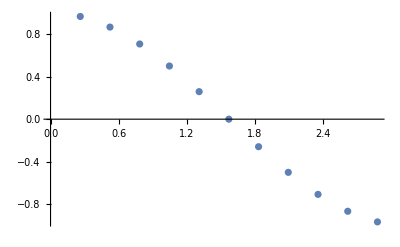

```mathematica
ListPlot[Table[{ThetaList[[i]],Cos[ThetaList[[i]]]},{i,1,11}]]
```

```mathematica
MinCosMat[l1_,l2_,μL_]:=Sum[(Factorial[l1]Factorial[l2])/(Factorial[n]Factorial[l1-n]Factorial[l2-n])((-(2π)/μL)^((l1+l2)/2-n)),{n,0,Min[l1,l2]}]
```

```mathematica
MinSinMat[l1_,l2_,μL_]:=√((2π)/μL)Sum[(Factorial[l1]Factorial[l2])/(Factorial[n]Factorial[l1-n]Factorial[l2-n])((-(2π)/μL)^((l1+l2-1)/2-n)),{n,0,Min[l1,l2]}]
```

```mathematica
Nmax=64;
```

```mathematica
e0p=Table[2i+1/2,{i,0,Nmax}];
H0p=DiagonalMatrix[e0p];
```

```mathematica
e0o=Table[2i+1+1/2,{i,0,Nmax}];
H0o=DiagonalMatrix[e0o];
```

```mathematica
SetUpMatricesToFile[L_,fname_]:=Module[{Mp,Mo,MSh},
Mp=Table[MinCosMat[2l1,2l2,L],{l1,0,Nmax},{l2,0,Nmax}];
M2p=Table[Chop[N[Mp[[i+1,j+1]]/√(Factorial[2i]Factorial[2j]),20]],{i,0,Nmax},{j,0,Nmax}];
Export[fname<>"mee",M2p,"Table","FieldSeparators"->" "];
Mo=Table[MinCosMat[2l1+1,2l2+1,L],{l1,0,Nmax},{l2,0,Nmax}];
M2o=Table[Chop[N[Mo[[i+1,j+1]]/√(Factorial[2i+1]Factorial[2j+1]),20]],{i,0,Nmax},{j,0,Nmax}];
Export[fname<>"moo",M2o,"Table","FieldSeparators"->" "];
MSh=Table[MinSinMat[2l1,2l2+1,L],{l1,0,Nmax},{l2,0,Nmax}];
M2Sh=Table[Chop[N[MSh[[i+1,j+1]]/√(Factorial[2i]Factorial[2j+1]),20]],{i,0,Nmax},{j,0,Nmax}];
Export[fname<>"meo",M2Sh,"Table","FieldSeparators"->" "];
]
```

```mathematica
SetUpMatrices[L_]:=Module[{Mp,Mo,MSh},
Mp=Table[MinCosMat[2l1,2l2,L],{l1,0,Nmax},{l2,0,Nmax}];
M2p=Table[zmu2[[L,2]]*N[Mp[[i+1,j+1]]/√(Factorial[2i]Factorial[2j]),20],{i,0,Nmax},{j,0,Nmax}];
Mo=Table[MinCosMat[2l1+1,2l2+1,L],{l1,0,Nmax},{l2,0,Nmax}];
M2o=Table[zmu2[[L,2]]*N[Mo[[i+1,j+1]]/√(Factorial[2i+1]Factorial[2j+1]),20],{i,0,Nmax},{j,0,Nmax}];
MSh=Table[MinSinMat[2l1,2l2+1,L],{l1,0,Nmax},{l2,0,Nmax}];
M2Sh=Table[zmu2[[L,2]]*N[MSh[[i+1,j+1]]/√(Factorial[2i]Factorial[2j+1]),20],{i,0,Nmax},{j,0,Nmax}];
]
```

```mathematica
First
```

```mathematica
SetUpMatrices[1];
```

```mathematica
(*-m mass: θ->π *)
```

```mathematica
CalculateMinSpace[m_,Nmax_,fname_]:=Module[{veigp,vveigp,vecp,evalvecp,veigo,vveigo,veco,evalveco,chmp,chmo,shm,test},
veigp=Sort[Eigenvalues[H0p+m*M2p]];
Export[fname<>"evalp",Take[veigp,11],"Table","FieldSeparators"->" "];
vveigp=Eigenvectors[H0p+m*M2p];
vecp=Table[Sign[vveigp[[Nmax+1-i,1]]]vveigp[[Nmax+1-i]],{i,0,10}];
evalvecp=Table[{vecp[[i]].(H0p+m*M2p).vecp[[i]],vecp[[i]]},{i,1,11}];
evalvecp=Sort[evalvecp,#1[[1]]<#2[[1]]&];

veigo=Sort[Eigenvalues[H0o+m*M2o]];
Export[fname<>"evalo",Take[veigo,11],"Table","FieldSeparators"->" "];
vveigo=Eigenvectors[H0o+m*M2o];
veco=Table[Sign[vveigo[[Nmax+1-i,1]]]vveigo[[Nmax+1-i]],{i,0,10}];
evalveco=Table[{veco[[i]].(H0o+m*M2o).veco[[i]],veco[[i]]},{i,1,11}];
evalveco=Sort[evalveco,#1[[1]]<#2[[1]]&];

chmp=Table[evalvecp[[i,2]].(M2p).evalvecp[[j,2]],{i,1,11},{j,1,11}];
Export[fname<>"chmp",chmp,"Table","FieldSeparators"->" "];
chmo=Table[evalveco[[i,2]].(M2o).evalveco[[j,2]],{i,1,11},{j,1,11}];
Export[fname<>"chmo",chmo,"Table","FieldSeparators"->" "];

shm=Table[evalvecp[[i,2]].(M2Sh).evalveco[[j,2]],{i,1,11},{j,1,11}];
Export[fname<>"shm",shm,"Table","FieldSeparators"->" "];

(*test=Sort[Eigenvalues[DiagonalMatrix[Take[veigp,11]]-m*chmp]];
Export[fname<> "test",test,"Table","FieldSeparators"->" "];*)
]
```

```mathematica
ThetaBl=DiagonalMatrix[Table[√(2j+1),{j,0,Nmax}]]+DiagonalMatrix[Table[√(2j),{j,1,Nmax}],-1];
```

```mathematica
ThetaBl//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√2 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | √5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √6 | √7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 √2 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √10 | √11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 √3 | √13 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √14 | √15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | √17)

```mathematica
CalculateMinSpace[m_,L_,θ_,Nmax_,fname_]:=Module[{H,veig,vveig,vec,evalvec,chm,shm},
H=ArrayFlatten[{{H0p+m*M2p,θ √(L/(8π))ThetaBl},{θ √(L/(8π))Transpose[ThetaBl],H0o+m*M2o}}] ;
veig=Sort[Eigenvalues[H]];
Export[fname<>"eval",Take[veig,21],"Table","FieldSeparators"->" "];
vveig=Eigenvectors[H];
vec=Table[Sign[vveig[[Nmax+1-i,1]]]vveig[[Nmax+1-i]],{i,0,20}];
evalvec=Table[{vec[[i]].(H).vec[[i]],vec[[i]]},{i,1,21}];
evalvec=Sort[evalvec,#1[[1]]<#2[[1]]&];

chm=Table[evalvec[[i,2]].ArrayFlatten[{{M2p,Table[0,{i,0,Nmax},{j,0,Nmax}]},{Table[0,{i,0,Nmax},{j,0,Nmax}],M2o}}].evalvec[[j,2]],{i,1,21},{j,1,21}];
Export[fname<>"chmp",chm,"Table","FieldSeparators"->" "];

shm=Table[evalvec[[i,2]].ArrayFlatten[{{Table[0,{i,0,Nmax},{j,0,Nmax}],M2Sh},{Transpose[M2Sh],Table[0,{i,0,Nmax},{j,0,Nmax}]}}].evalvec[[j,2]],{i,1,21},{j,1,21}];
Export[fname<>"shm",shm,"Table","FieldSeparators"->" "];
]
```

```mathematica
SetUpMatrices[1];
veigo=Sort[Eigenvalues[H0o+m*M2o]];
vveigo=Sort[Eigenvectors[H0o+m*M2o]];
veco=Table[Sign[vveigo[[Nmax+1-i,1]]]vveigo[[Nmax+1-i]],{i,0,10}];
evalveco=Table[{veco[[i]].(H0o+m*M2o).veco[[i]],veco[[i]]},{i,1,11}];
evalveco=Sort[evalveco,#1[[1]]<#2[[1]]&];
```

```mathematica
CreateDirectory["test"]
```

/home/raynor/ZeroMode/test

```mathematica
SetDirectory["test"]
```

```mathematica
DirectoryQ["th0"]
```

True

```mathematica
For[n=16, n≤128,n=n*2,
{
Nmax=n;
e0p=Table[2i+1/2,{i,0,Nmax}];
H0p=DiagonalMatrix[e0p];
e0o=Table[2i+1+1/2,{i,0,Nmax}];
H0o=DiagonalMatrix[e0o];
Print[SetUpMatrices[1]//Timing];
dname="th0m1c"<>ToString[n];
Print[CalculateMinSpace[2.0,Nmax,dname]//Timing]
}]
```

{0.271956,Null}

{0.175359,Null}

{2.60574,Null}

{0.310773,Null}

{14.6633,Null}

{1.07261,Null}

{110.994,Null}

{3.83553,Null}

```mathematica
Directory[]
```

/home/raynor/th2/m10

```mathematica
SetDirectory["/home/raynor/ZeroMode"]
```

/home/raynor/ZeroMode

```mathematica
(* θ függés *)
```

```mathematica
For[l=1, l≤20,l++,
{
Print[SetUpMatricesToFile[l,"l"<>ToString[l]]//Timing]
}
]
```

{107.001,Null}

{102.151,Null}

{127.634,Null}

{117.798,Null}

{134.687,Null}

{126.479,Null}

{132.701,Null}

{119.236,Null}

{134.294,Null}

{130.192,Null}

{136.924,Null}

{130.172,Null}

{138.043,Null}

{133.572,Null}

{140.679,Null}

{131.352,Null}

{144.241,Null}

{136.263,Null}

{141.812,Null}

{136.346,Null}

```mathematica
For[l=1, l≤20,l++,
{
Print[SetUpMatrices[l]//Timing]
For[j=1, j≤11,j++,
{
If [!DirectoryQ["th"<>ToString[j]],CreateDirectory["th"<>ToString[j]]];
SetDirectory["th"<>ToString[j]];
For[i=1, i≤12, i++,
{
If[!DirectoryQ["m"<>ToString[i]],CreateDirectory["m"<>ToString[i]]];
SetDirectory["m"<>ToString[i]];
dname="th"<>ToString[j]<>"m"<>ToString[i]<>"L"<>ToString[l];
Print[CalculateMinSpace[massList[[i]],l,ThetaList[[j]],Nmax,dname]//Timing];
SetDirectory[ParentDirectory[]]
}]
SetDirectory[ParentDirectory[]]
}]
}]
```

```mathematica
Directory[]
```

/home/raynor/ZeroMode/th00L40/m8

```mathematica
SetDirectory[ParentDirectory[]]
```

/home/raynor/ZeroMode

```mathematica
SetDirectory["th00L40_64"]
```

/home/raynor/ZeroMode/th00L40_64

```mathematica
S
```

```mathematica
(* parity figyelembe vétel, legutóbb θ=0 *)
```

```mathematica
For[l=21, l≤40,l++,
{
Print[SetUpMatrices[l]//Timing]
For[i=6, i≤6, i++,
{
If[!DirectoryQ["m"<>ToString[i]],CreateDirectory["m"<>ToString[i]]];
SetDirectory["m"<>ToString[i]];
dname="th0m"<>ToString[i]<>"L"<>ToString[l];
Print[CalculateMinSpace[massList[[i]]*l,Nmax,dname]//Timing];
SetDirectory[ParentDirectory[]]
}
 ]
}
]
```

{16.5986,Null}

{0.869209,Null}

{16.7558,Null}

{0.841151,Null}

{16.9138,Null}

{0.711411,Null}

{16.648,Null}

{0.864512,Null}

{16.7227,Null}

{0.851618,Null}

{16.4972,Null}

{0.880244,Null}

{17.179,Null}

{0.8944,Null}

{16.8885,Null}

{0.928849,Null}

{16.9684,Null}

{0.870804,Null}

{16.8089,Null}

{0.867243,Null}

{17.311,Null}

{0.907113,Null}

{15.4694,Null}

{0.86073,Null}

{17.2622,Null}

{0.874305,Null}

{17.0215,Null}

{0.853957,Null}

{17.3554,Null}

{0.718526,Null}

{17.0171,Null}

{0.805256,Null}

{17.1913,Null}

{0.734578,Null}

{16.7579,Null}

{0.8772,Null}

{16.9742,Null}

{0.938842,Null}

{16.8927,Null}

{0.88797,Null}

```mathematica
CalculateMinSpace[-1,Nmax,"fout"]//Timing
```

{9.45033,Null}

```mathematica
CalculateMinSpace[1,1,π/2,Nmax,"fth"]//Timing
```

{40.8803,Null}

```mathematica
t1={1,2,3,4,5};
t2={{2,3},{1,4},{4,1},{3,9},{5,0}};
```

```mathematica
t2=Sort[t2,#1[[1]]<#2[[1]]&]
```

{{1,4},{2,3},{3,9},{4,1},{5,0}}

```mathematica
t1[[1]]
```

1

```mathematica
FirstPosition[t2,1]
```

{2}

```mathematica
Table[FirstPosition[t2,t1[[i]]],{i,1,5}]//Flatten
```

{2,1,4,3,5}

```mathematica
Which
```

```mathematica
Print[a]; Print[b];
```

a

b

```mathematica
Length[H0p]
```

21

```mathematica
L=5;
```

```mathematica
Mp=Table[MinCosMat[2l1,2l2,L],{l1,0,Nmax},{l2,0,Nmax}];
M2p=Table[zmu[[L,2]]N[Mp[[i+1,j+1]]/√(Factorial[2i]Factorial[2j]),20],{i,0,Nmax},{j,0,Nmax}];
Mo=Table[MinCosMat[2l1+1,2l2+1,L],{l1,0,Nmax},{l2,0,Nmax}];
M2o=Table[zmu[[L,2]]N[Mo[[i+1,j+1]]/√(Factorial[2i+1]Factorial[2j+1]),20],{i,0,Nmax},{j,0,Nmax}];
```

```mathematica
H=ArrayFlatten[{{H0p,θ √(L/(8π))ThetaBl},{θ √(L/(8π))Transpose[ThetaBl],H0o}}]/.θ->0;
```